#### Problem 7.5.30b

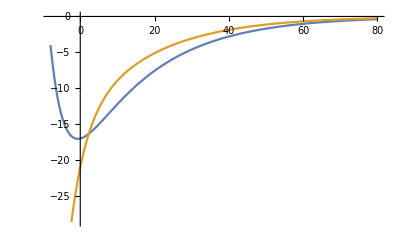

```mathematica
Plot[{(-3*55/8)*Exp[-0.05t]+(29/8)*Exp[-0.25t],(-2*55/8)*Exp[-0.05t]+(-2*29/8)*Exp[-0.25t]},{t,-8,80}]
```

```mathematica
Solve[{Abs[(-3*55/8)*Exp[-0.05t]+(29/8)*Exp[-0.25t]]≤0.5, Abs[(-2*55/8)*Exp[-0.05t]+(-2*29/8)*Exp[-0.25t]]≤0.5},{t}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[{Abs[(29 ⅇ^(-0.25 t))/8-(165 ⅇ^(-0.05 t))/8]≤0.5,Abs[-29/4 ⅇ^(-0.25 t)-(55 ⅇ^(-0.05 t))/4]≤0.5},{t}]

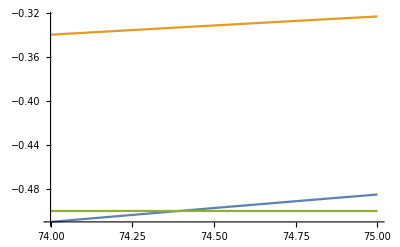

```mathematica
Plot[{(-3*55/8)*Exp[-0.05t]+(29/8)*Exp[-0.25t],(-2*55/8)*Exp[-0.05t]+(-2*29/8)*Exp[-0.25t],-0.5},{t,74,75}]
```

#### 7.5.31

```mathematica
Manipulate[StreamPlot[{-x-a*y,-x-y},{x,-10,10},{y,-10,10}], {a,0.5,2}]
```

#### 7.6.14

Part c

```mathematica
Manipulate[StreamPlot[{-5y,x+a*y},{x,-20,20},{y,-20,20}],{a,-5,5}]
```

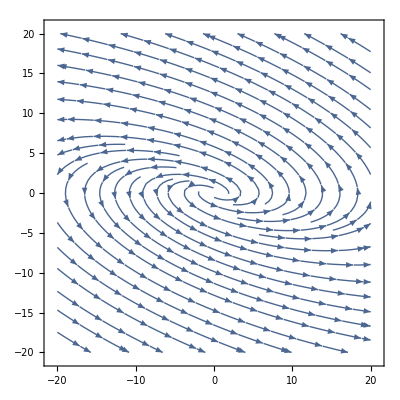

```mathematica
StreamPlot[{-5y,x+2*y},{x,-20,20},{y,-20,20}]
```

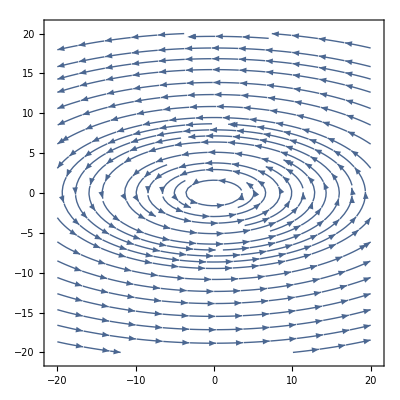

```mathematica
StreamPlot[{-5y,x},{x,-20,20},{y,-20,20}]
```

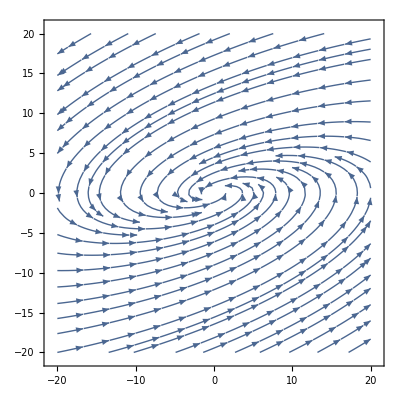

```mathematica
StreamPlot[{-5y,x-2*y},{x,-20,20},{y,-20,20}]
```

#### 7.8.1a

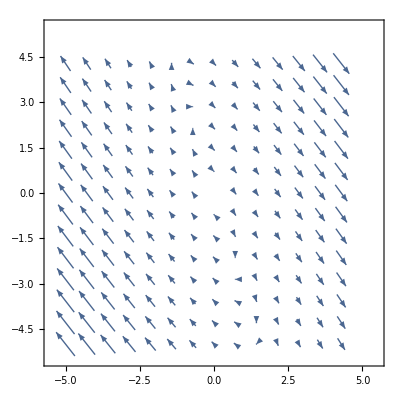
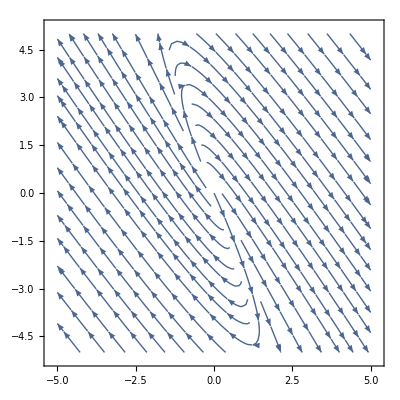

```mathematica
Overlay[{VectorPlot[{3x+y,-4x-y},{x,-5,5},{y,-5,5}],StreamPlot[{3x+y,-4x-y},{x,-5,5},{y,-5,5}]}]
```

#### 7.8.7b

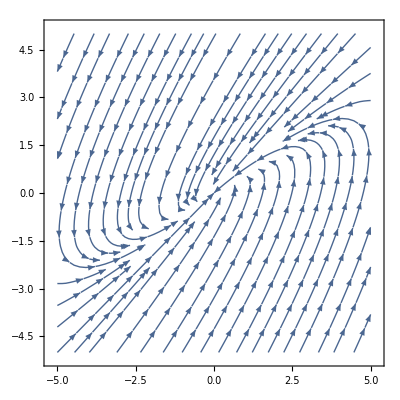
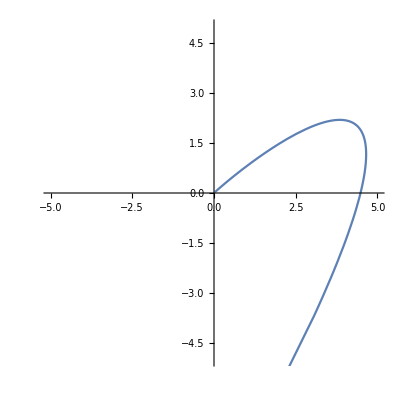

```mathematica
Overlay[{StreamPlot[{x-4y,4x-7y},{x,-5,5},{y,-5,5}],ParametricPlot[{Exp[-3t]*((4*t)+3),Exp[-3t]*((4*t)+2)}, {t,-1,2}, PlotRange->{{-5,5},{-5,5}}]}]
```

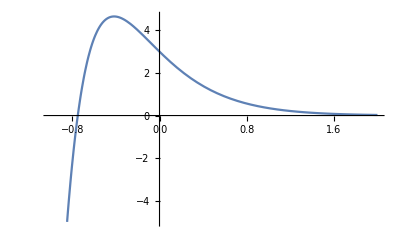

```mathematica
Plot[Exp[-3t]*(4t+3), {t,-1,2}]
```

#### 7.8.9b

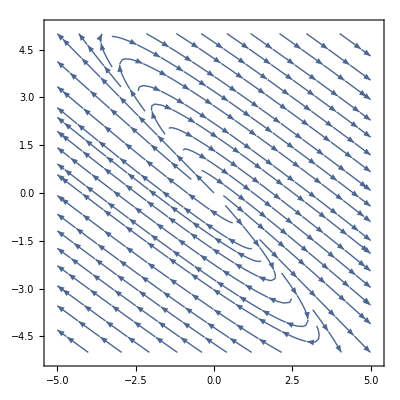
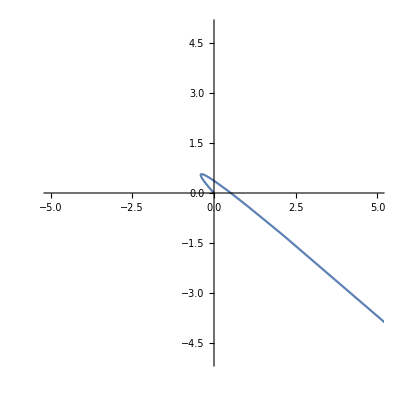

```mathematica
Overlay[{StreamPlot[{2x+(3/2)y,(-3/2)x-y},{x,-5,5},{y,-5,5}],ParametricPlot[{Exp[t/2]*(3+(3t/2)),Exp[t/2]*(-2-(3t/2))}, {t,-200,3}, PlotRange->{{-5,5},{-5,5}}]}]
```

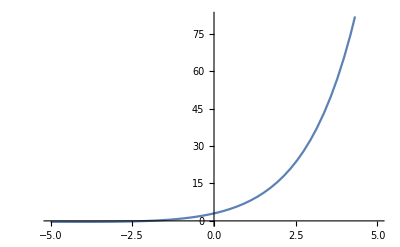

```mathematica
Plot[Exp[t/2]*(3+(3t/2)),{t,-5,5}]
```